```mathematica
Clear["Global`*"];
pl=Plot3D[z=0,{x,-4,4},{y,-4,4}];
Show[pl]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x ]+Sin[y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Subscript[p, 1]={1,0,0};
Subscript[r, 1]=1;
Subscript[p, 2]={3,0,0};
Subscript[r, 2]=2;
obs=Graphics3D[{
Sphere[Subscript[p, 1],Subscript[r, 1]],
Sphere[Subscript[p, 2],Subscript[r, 2]],

},Axes->True];
Show[{obs}]
Show[{pl,obs}]
```

-Graphics3D-

-Graphics3D-

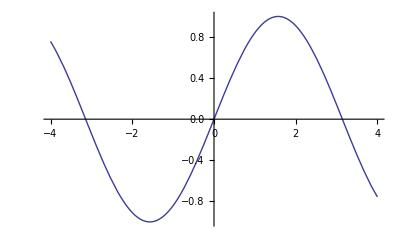

```mathematica
Plot[{Sin[α]},{α,-4,4}]
```

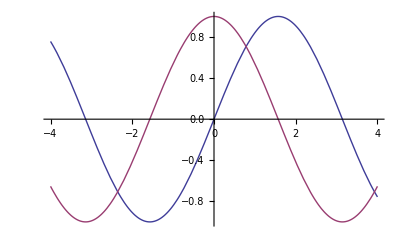

```mathematica
Plot[{Sin[α],Cos[α]},{α,-4,4}]
```

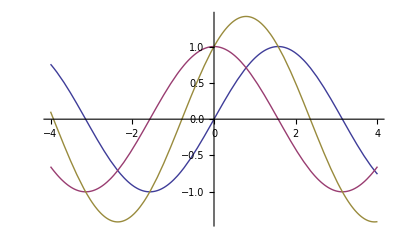

```mathematica
Plot[{Sin[α],Cos[α],Sin[α]+Cos[α]},{α,-4,4}]
```

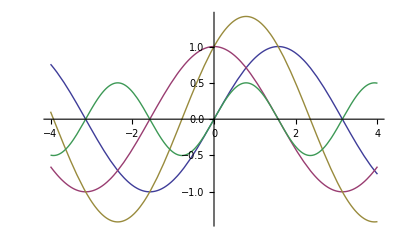

```mathematica
Plot[{Sin[α],Cos[α],Sin[α]+Cos[α],Sin[α]*Cos[α]},{α,-4,4}]
```

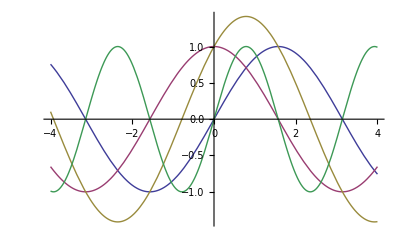

```mathematica
Plot[{Sin[α],Cos[α],Sin[α]+Cos[α],2*Sin[α]*Cos[α]},{α,-4,4}]
```

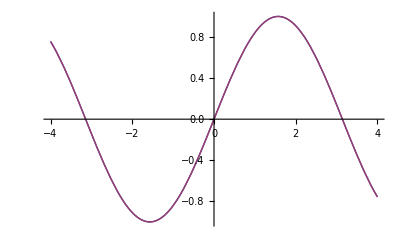

```mathematica
Plot[{Sin[α],2*Sin[α/2]*Cos[α/2]},{α,-4,4}]
```

```mathematica
Sin[α]==2*Sin[α/2]*Cos[α/2]
```

Sin[α]==2 Cos[α/2] Sin[α/2]

```mathematica
Plot[{Sin[α],-1+8(Sin[α/4+π/8]*Cos[α/4+π/8])^2},{α,-4,4}]
```

-Graphics-